```mathematica
Clear["Global`*"]
Needs["ErrorBarPlots`"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
npart=3;
nd=3;
nbead=16;
nperm=2;
beadexp=Log[2,nbead];
βmax = 10.0;
βmin=0.1;
```

```mathematica
z0[β_,ω_,d_]:=(1/(2 Sinh[(β ℏ ω)/2]))^d/.{ℏ-> 1,m-> 1};
z[N_,β_,ω_,d_]:=If[N==0,1,1/N Sum[(-1)^(n-1)z0[n β,ω,d]z[N-n,β,ω,d],{n,1,N}]];
e[N_,β_,ω_,d_]:=-1/z[N,β,ω,d]D[z[N,β,ω,d],β];
```

```mathematica
e1=e[1,β,1,nd];
e1limit=Limit[e0,β-> ∞];
e3=e[3,β,1,nd];
e3limit=Limit[e3,β-> ∞];
z1=z[1,β,1,nd];
z3=z[3,β,1,nd];
```

```mathematica
For[j=0,j<nperm,j++,edata[j]=Import[StringJoin["Fermions/epoints",ToString[npart],"-",ToString[nd],"-",ToString[2^beadexp],"-",ToString[j],".dat"]]]
edata[nperm] = Import[StringJoin["Fermions/epoints",ToString[npart],"-",ToString[nd],"-",ToString[2^beadexp],".dat"]];
For[j=0,j≤nperm,j++,epoints[j]=Table[edata[j][[i,2]],{i,1,Length[edata[j]]}]]
```

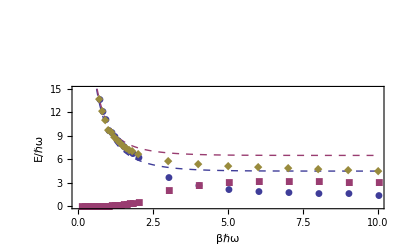

```mathematica
modelePlot=Plot[{3.0e1,e3},{β,0,βmax},PlotRange-> {0,15},PlotStyle->Dashed];
pointsePlot=ListPlot[Table[edata[j],{j,0,nperm}],PlotStyle->Thick,PlotMarkers-> Automatic];
Show[modelePlot,pointsePlot,LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel-> False,Frame->True,FrameLabel-> {Style["βℏω",Bold],Style["E/ℏω",Bold]}]
```

Numerical Integration Methods

```mathematica
euler[f_,{x_,x0_,xn_},{y_,y0_},steps_]:=Block[{xold=x0,yold=y0,sollist={{x0,y0}},x,y,h},h=N[(xn-x0)/steps];
Do[xnew=xold+h;
ynew=yold+h*(f/.{x->xold,y->yold});
sollist=Append[sollist,{xnew,ynew}];
xold=xnew;
yold=ynew,{steps}];
Return[sollist]]
```

```mathematica
heun[f_,{x_,x0_,xn_},{y_,y0_},steps_]:=Block[{xold=x0,yold=y0,sollist={{x0,y0}},x,y,h},h=N[(xn-x0)/steps];
Do[xnew=xold+h;
slopeold=f/.{x->xold,y->yold};
slopenew=f/.{x->(xold+h),y->(yold+h*(f/.{x->xold,y->yold}))};
ynew=yold+0.5*h*(slopeold+slopenew);
sollist=Append[sollist,{xnew,ynew}];
xold=xnew;
yold=ynew,{steps}];
Return[sollist]]
```

```mathematica
RKA[f_,{x_,x0_,xn_},{y_,y0_},steps_]:=Block[{xold=x0,yold=y0,sollist={{x0,y0}},x,y,h},h=N[(xn-x0)/steps];
Do[xnew=xold+h;
k1=h*f/.{x->xold,y->yold};
k2=h*f/.{x->(xold+0.5*h),y->(yold+0.5*k1)};
k3=h*f/.{x->(xold+0.5*h),y->(yold+0.5*k2)};
k4=h*f/.{x->(xold+h),y->(yold+k3)};
ynew=yold+(1.0/6.0)*(k1+2k2+2k3+k4);
sollist=Append[sollist,{xnew,ynew}];
xold=xnew;
yold=ynew,{steps}];
Return[sollist]]
```

## 1

```mathematica
f1pts=Table[{edata[0][[i,1]],3(e1/.β-> edata[0][[i,1]])},{i,1,Length[edata[0]]}];h1pts=Table[{edata[0][[i,1]],-6edata[0][[i,2]](z3/z1^3/.β-> edata[0][[i,1]])},{i,1,Length[edata[0]]}];
```

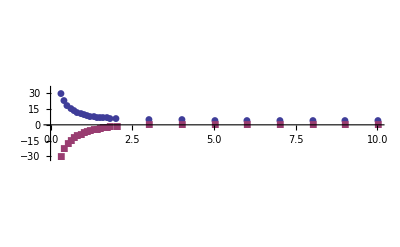

```mathematica
ListPlot[{f1pts,h1pts},AxesOrigin-> {0,0},PlotStyle->Thick,PlotMarkers-> Automatic]
```

```mathematica
f1=Interpolation[f1pts];
f1b[β]=e1;
h1=Interpolation[h1pts];
```

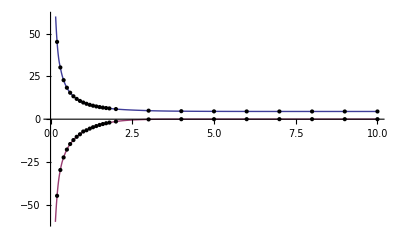

```mathematica
Plot[{f1[β],h1[β]},{β,0.1,10.0},Epilog->Map[Point,{f1pts,h1pts}],AxesOrigin-> {0,0},PlotStyle->Thick,PlotRange->{-60,60}]
```

```mathematica
f[β_,Ω1_]:=f1[β]Ω1+h1[β];
Ω10=1.0;
β0=0.1;
βN=1.0;
nsteps=100;
eulersol1=euler[f[β,Ω1],{β,β0,βN},{Ω1,Ω10},nsteps];
heunsol1=heun[f[β,Ω1],{β,β0,βN},{Ω1,Ω10},nsteps];
RKAsol1=RKA[f[β,Ω1],{β,β0,βN},{Ω1,Ω10},nsteps];
```

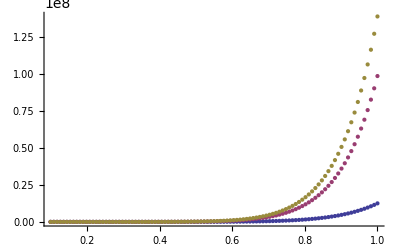

```mathematica
ListPlot[{eulersol1,heunsol1,RKAsol1}]
```

```mathematica
Ω1ndsol=NDSolve[{Ω1'[β]==f1[β]Ω1[β]+h1[β],Ω1[10]==0.0},Ω1,{β,0.1,10}];
```

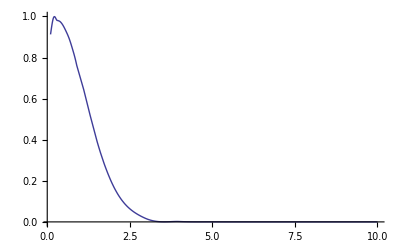

```mathematica
Plot[Ω1[β]/.Ω1ndsol,{β,0.1,10},PlotRange-> {0.0,1.0}]
```

## 2

```mathematica
f2pts=Table[{edata[1][[i,1]],3.0(e1/.β-> 3edata[1][[i,1]])},{i,1,Length[edata[1]]}];h2pts=Table[{edata[1][[i,1]],-3.0edata[1][[i,2]]((z3/.β-> edata[1][[i,1]])/(z1/.β-> 3edata[1][[i,1]]))},{i,1,Length[edata[1]]}];
```

```mathematica
h2pts={{0.1,0},{0.2,0},{0.3,0},{0.4,-0.5455786692713708},{0.5,-0.3751598795360178},{0.6,-0.5741956190237169},{0.7,-0.623667150879766},{0.8,-0.9002226881199586},{0.9,-0.79880599658753},{1.1,-0.6949902482989467},{1.2,-0.6264466211012241},{1.3,-0.5210100335504474},{1.4,-0.41865744876029104},{1.5,-0.4246785114901881},{1.6,-0.3631195554464433},{1.7,-0.33500921397874023},{1.8,-0.28162736758650886},{2,-0.21399258358688134},{3,-0.06382430199454872},{4,-0.00923269815113272},{5,-0.0012796005447990788},{6,-0.00017565360673267298},{7,-0.000024226079040283485},{8,-3.2159349611848515*^-6},{9,-4.26148564295496*^-7},{10,-5.71868645514079*^-8}};
```

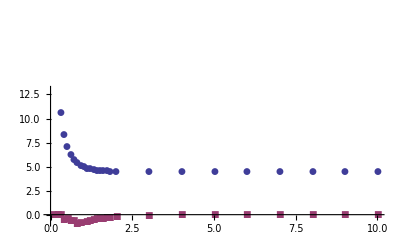

```mathematica
ListPlot[{f2pts,h2pts},AxesOrigin-> {0,0},PlotStyle->Thick,PlotMarkers-> Automatic]
```

```mathematica
f2=Interpolation[f2pts];
f2b[β]=e1/.β-> 3β;
h2=Interpolation[h2pts];
```

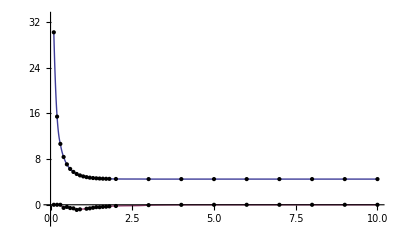

```mathematica
Plot[{f2[β],h2[β]},{β,0.1,10.0},Epilog->Map[Point,{f2pts,h2pts}],AxesOrigin-> {0,0},PlotStyle->Thick,PlotRange->{-3,33}]
```

```mathematica
g[β_,Ω2_]:=f2[β]Ω2+h2[β];
Ω20=0.0;
β0=0.1;
βN=10.0;
nsteps=100;
```

```mathematica
eulersol2=euler[g[β,Ω2],{β,β0,βN},{Ω2,Ω20},nsteps];
heunsol2=heun[g[β,Ω2],{β,β0,βN},{Ω2,Ω20},nsteps];
RKAsol2=RKA[g[β,Ω2],{β,β0,βN},{Ω2,Ω20},nsteps];
```

```mathematica
ListPlot[{eulersol2,heunsol2,RKAsol2}]
```

-Graphics-

```mathematica
Ω2ndsol=NDSolve[{Ω2'[β]==f2[β]Ω2[β]+h2[β],Ω2[10.0]==0.0},Ω2,{β,0.1,10}];
```

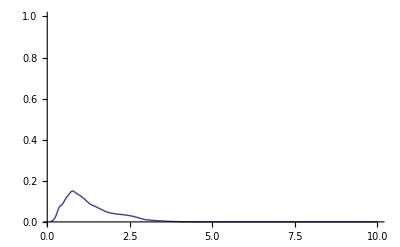

```mathematica
Plot[Ω2[β]/.Ω2ndsol,{β,0.1,10},PlotRange-> {0.0,1.0}]
```

## Checks

```mathematica
z13=z1/.{β->3β};
z12=z1/.{β->2β};
```

```mathematica
α=2.0;
```

```mathematica
z3/.{β->α}
```

0.0000166833

```mathematica
z1^3/.{β->α}
```

0.000456794

```mathematica
z13/.{β->α}
```

0.000124332

```mathematica
z1 z12/.{β->α}
```

0.000201786

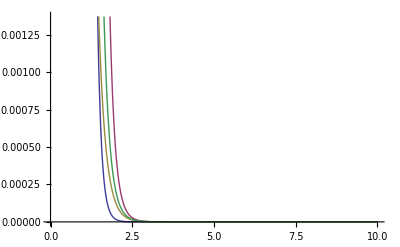

```mathematica
Plot[{z3,z1^3,z13,z1 z12},{β,0,10},PlotStyle->Thick]
```

```mathematica
z3sol=1/6(Ω1[β]/.Ω1ndsol)z1^3+1/3(Ω2[β]/.Ω2ndsol)z13;
```

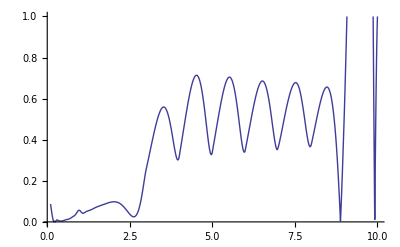

```mathematica
Plot[Abs[z3-z3sol]/z3,{β,0.1,10},PlotStyle->Thick,PlotRange-> {0,1}]
```

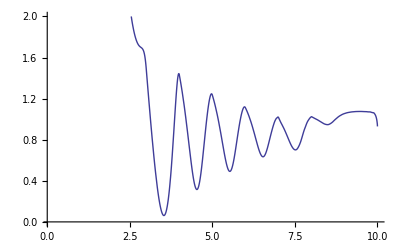

```mathematica
Plot[{(Ω1[β]/.Ω1ndsol)/(Ω2[β]/.Ω2ndsol)},{β,0.1,10},PlotStyle->Thick,PlotRange-> {0,2}]
```